```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/mma/dispersion-relation/boxspectrum

```mathematica
Get["../../../neupackage/mma/dispersion-relation.wl"]
```

```mathematica
spectWC1={{{-1,-0.3},1},{{-0.3,1},1}};
spectWC2={{{-1,-0.3},0.5},{{-0.3,1},1}};
spectWC3={{{-1,-0.3},0.1},{{-0.3,1},1}};
spectWC4={{{-1,-0.3},0},{{-0.3,1},1}};
```

```mathematica
spectC1={{{-1,-0.3},-0.1},{{-0.3,1},1}};
spectC2={{{-1,-0.3},-0.5},{{-0.3,1},1}};
spectC3={{{-1,-0.3},-1},{{-0.3,1},1}};
spectC4={{{-1,-0.3},-1.5},{{-0.3,1},1}};
```

```mathematica
spectAbs={{{c1,c0},g1},{{c0,c2},g2}}
spectAbs2={{{-1,-0.3},g1},{{-0.3,1},1}};
```

{{{c1,c0},g1},{{c0,c2},g2}}

```mathematica
eqn=ConAxialSymOmegaNMZASQRT[n,spectAbs]==0;
```

```mathematica
Solve[eqn,g1]
```

{{g1→(g2 (2 c0 n-2 c2 n+4 c0 n^2+c0^2 n^2-4 c2 n^2-c2^2 n^2+2 n^2 Log[(1-c0 n)/(1-c2 n)]-2 Log[(-1+c2 n)/(-1+c0 n)]-4 n Log[(-1+c2 n)/(-1+c0 n)]))/(n^2 (4 c0+c0^2-4 c1-c1^2+(2 c0)/n-(2 c1)/n-2 Log[(1-c1 n)/(1-c0 n)]+(2 Log[(-1+c0 n)/(-1+c1 n)])/n^2+(4 Log[(-1+c0 n)/(-1+c1 n)])/n))},{g1→(g2 (2 c0 n-2 c2 n-4 c0 n^2+c0^2 n^2+4 c2 n^2-c2^2 n^2+2 n^2 Log[(1-c0 n)/(1-c2 n)]-2 Log[(-1+c2 n)/(-1+c0 n)]+4 n Log[(-1+c2 n)/(-1+c0 n)]))/(n^2 (-4 c0+c0^2+4 c1-c1^2+(2 c0)/n-(2 c1)/n-2 Log[(1-c1 n)/(1-c0 n)]+(2 Log[(-1+c0 n)/(-1+c1 n)])/n^2-(4 Log[(-1+c0 n)/(-1+c1 n)])/n))}}

Define the function under the square root

```mathematica
Reduce[
ConAxialSymOmegaNMZASQRT[n,spectAbs2]==0,g1
]
```

$Aborted

```mathematica
spectG1[n_]=g1/.Solve[
ConAxialSymOmegaNMZASQRT[n,spectAbs2]==0,g1
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{(260. n+611. n^2-200. n^2 Log[(1.+0.3 n)/(1.-1. n)]+200. Log[(-1.+n)/(-1.-0.3 n)]+400. n Log[(-1.+n)/(-1.-0.3 n)])/(-140. n-189. n^2-200. Log[(-1.-0.3 n)/(-1.-1. n)]-400. n Log[(-1.-0.3 n)/(-1.-1. n)]+200. n^2 Log[(1.+n)/(1.+0.3 n)]),(260. n-429. n^2-200. n^2 Log[(1.+0.3 n)/(1.-1. n)]+200. Log[(-1.+n)/(-1.-0.3 n)]-400. n Log[(-1.+n)/(-1.-0.3 n)])/(-140. n+371. n^2-200. Log[(-1.-0.3 n)/(-1.-1. n)]+400. n Log[(-1.-0.3 n)/(-1.-1. n)]+200. n^2 Log[(1.+n)/(1.+0.3 n)])}

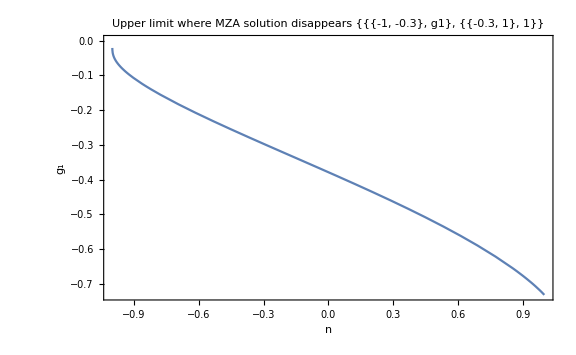

```mathematica
Plot[spectG1[n][[2]],{n,-2,2},PlotRange->{Automatic,Automatic},Frame->True,ImageSize->Large,PlotLabel->"Upper limit where MZA solution disappears "<>ToString[spectAbs2],FrameLabel->{"n","g_1"}]
```

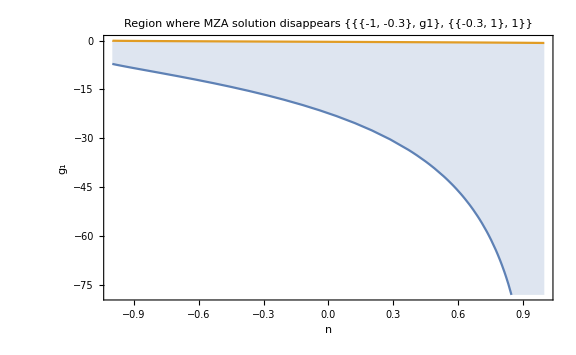

```mathematica
Plot[{spectG1[n][[1]],spectG1[n][[2]]},{n,-2,2},PlotRange->{Automatic,Automatic},Frame->True,Filling->{1->{2}},ImageSize->Large,PlotLabel->"Region where MZA solution disappears "<>ToString[spectAbs2],FrameLabel->{"n","g_1"}]
```

```mathematica
spectG1[#]&/@{-1,1}
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}

```mathematica
Limit[spectG1[n],n->#]&/@{-1,1}
```

{{-7.16327,0.},{-∞,-0.731602-5.43999 ⅈ}}

```mathematica
spectG1[0.999999999999999]
```

{-1725.97,-0.731602}

Check Taylor Expansion

```mathematica
Series[
ConAxialSymOmegaNMZA[n,spectAbs],
{g1,0,2}
]//Simplify
```

{1/(8 n^3)(-2 c0 g2 n+2 c2 g2 n-c0^2 g2 n^2+c2^2 g2 n^2+2 g2 n^2 Log[(-1+c0 n)/(-1+c2 n)]+2 g2 Log[(-1+c2 n)/(-1+c0 n)]-n^3 √(1/n^6 g2^2 ((c0-c2) n (2+(4+c0+c2) n)+2 n^2 Log[(-1+c0 n)/(-1+c2 n)]-2 (1+2 n) Log[(-1+c2 n)/(-1+c0 n)]) ((c0-c2) n (2+(-4+c0+c2) n)+2 n^2 Log[(-1+c0 n)/(-1+c2 n)]+(-2+4 n) Log[(-1+c2 n)/(-1+c0 n)])))+1/(8 n^3)(2 c0 n-2 c1 n+c0^2 n^2-c1^2 n^2+2 Log[(-1+c0 n)/(-1+c1 n)]+2 n^2 Log[(-1+c1 n)/(-1+c0 n)]+(g2 (2 Log[(-1+c0 n)/(-1+c1 n)] (n (c0^2 n+c0 (2-8 n^2)-c2 (2+c2 n-8 n^2))+2 n^2 Log[(-1+c0 n)/(-1+c2 n)]+(-2+8 n^2) Log[(-1+c2 n)/(-1+c0 n)])+n (2 n Log[(-1+c1 n)/(-1+c0 n)] (-(c0-c2) n (2+c0 n+c2 n)-2 n^2 Log[(-1+c0 n)/(-1+c2 n)]+2 Log[(-1+c2 n)/(-1+c0 n)])+(c0-c1) ((c0-c2) n (c0^2 n^2+c1 n (2+c2 n)+c0 n (4+c1 n+c2 n)+2 (2+c2 n-8 n^2))+2 n^2 (2+c0 n+c1 n) Log[(-1+c0 n)/(-1+c2 n)]-2 (2+c0 n+c1 n-8 n^2) Log[(-1+c2 n)/(-1+c0 n)]))))/(n^3 √(1/n^6 g2^2 ((c0-c2) n (2+(4+c0+c2) n)+2 n^2 Log[(-1+c0 n)/(-1+c2 n)]-2 (1+2 n) Log[(-1+c2 n)/(-1+c0 n)]) ((c0-c2) n (2+(-4+c0+c2) n)+2 n^2 Log[(-1+c0 n)/(-1+c2 n)]+(-2+4 n) Log[(-1+c2 n)/(-1+c0 n)])))) g1+(g2^2 (Log[(-1+c0 n)/(-1+c1 n)] (-c0^2+c2^2-2 Log[(-1+c0 n)/(-1+c2 n)])+2 Log[(-1+c1 n)/(-1+c0 n)] ((-c0+c2) n+Log[(-1+c2 n)/(-1+c0 n)])+(c0-c1) ((c0-c2) (c1-c2) n-2 n Log[(-1+c0 n)/(-1+c2 n)]-(c0+c1) Log[(-1+c2 n)/(-1+c0 n)]))^2 g1^2)/(n^6 (1/n^6 g2^2 ((c0-c2) n (2+(4+c0+c2) n)+2 n^2 Log[(-1+c0 n)/(-1+c2 n)]-2 (1+2 n) Log[(-1+c2 n)/(-1+c0 n)]) ((c0-c2) n (2+(-4+c0+c2) n)+2 n^2 Log[(-1+c0 n)/(-1+c2 n)]+(-2+4 n) Log[(-1+c2 n)/(-1+c0 n)]))^(3/2))+O[g1]^3,1/(8 n^3)(-2 c0 g2 n+2 c2 g2 n-c0^2 g2 n^2+c2^2 g2 n^2+2 g2 n^2 Log[(-1+c0 n)/(-1+c2 n)]+2 g2 Log[(-1+c2 n)/(-1+c0 n)]+n^3 √(1/n^6 g2^2 ((c0-c2) n (2+(4+c0+c2) n)+2 n^2 Log[(-1+c0 n)/(-1+c2 n)]-2 (1+2 n) Log[(-1+c2 n)/(-1+c0 n)]) ((c0-c2) n (2+(-4+c0+c2) n)+2 n^2 Log[(-1+c0 n)/(-1+c2 n)]+(-2+4 n) Log[(-1+c2 n)/(-1+c0 n)])))+1/(8 n^6)(n^3 ((c0-c1) n (2+c0 n+c1 n)+2 Log[(-1+c0 n)/(-1+c1 n)])+2 n^5 Log[(-1+c1 n)/(-1+c0 n)]-(g2 (2 Log[(-1+c0 n)/(-1+c1 n)] (n (c0^2 n+c0 (2-8 n^2)-c2 (2+c2 n-8 n^2))+2 n^2 Log[(-1+c0 n)/(-1+c2 n)]+(-2+8 n^2) Log[(-1+c2 n)/(-1+c0 n)])+n (2 n Log[(-1+c1 n)/(-1+c0 n)] (-(c0-c2) n (2+c0 n+c2 n)-2 n^2 Log[(-1+c0 n)/(-1+c2 n)]+2 Log[(-1+c2 n)/(-1+c0 n)])+(c0-c1) ((c0-c2) n (c0^2 n^2+c1 n (2+c2 n)+c0 n (4+c1 n+c2 n)+2 (2+c2 n-8 n^2))+2 n^2 (2+c0 n+c1 n) Log[(-1+c0 n)/(-1+c2 n)]-2 (2+c0 n+c1 n-8 n^2) Log[(-1+c2 n)/(-1+c0 n)]))))/(√(1/n^6 g2^2 ((c0-c2) n (2+(4+c0+c2) n)+2 n^2 Log[(-1+c0 n)/(-1+c2 n)]-2 (1+2 n) Log[(-1+c2 n)/(-1+c0 n)]) ((c0-c2) n (2+(-4+c0+c2) n)+2 n^2 Log[(-1+c0 n)/(-1+c2 n)]+(-2+4 n) Log[(-1+c2 n)/(-1+c0 n)])))) g1-(g2^2 (Log[(-1+c0 n)/(-1+c1 n)] (-c0^2+c2^2-2 Log[(-1+c0 n)/(-1+c2 n)])+2 Log[(-1+c1 n)/(-1+c0 n)] ((-c0+c2) n+Log[(-1+c2 n)/(-1+c0 n)])+(c0-c1) ((c0-c2) (c1-c2) n-2 n Log[(-1+c0 n)/(-1+c2 n)]-(c0+c1) Log[(-1+c2 n)/(-1+c0 n)]))^2 g1^2)/(n^6 (1/n^6 g2^2 ((c0-c2) n (2+(4+c0+c2) n)+2 n^2 Log[(-1+c0 n)/(-1+c2 n)]-2 (1+2 n) Log[(-1+c2 n)/(-1+c0 n)]) ((c0-c2) n (2+(-4+c0+c2) n)+2 n^2 Log[(-1+c0 n)/(-1+c2 n)]+(-2+4 n) Log[(-1+c2 n)/(-1+c0 n)]))^(3/2))+O[g1]^3}

```mathematica
mzaSeries[n_]=Normal[
Series[
ConAxialSymOmegaNMZA[n,spectAbs2],
{g1,0,2}
]//Simplify
]
```

{1/n^3(0.325 n+0.11375 n^2+0.25 Log[(-1+n)/(-1-0.3 n)]+0.25 n^2 Log[(-1.-0.3 n)/(-1.+n)]-0.25 n^3 √((((-1.3-3.055 n) n+1. n^2 Log[(1.+0.3 n)/(1.-1. n)]+(-1.-2. n) Log[(-1.+n)/(-1.-0.3 n)]) (n (-1.3+2.145 n)+1. n^2 Log[(1.+0.3 n)/(1.-1. n)]+(-1.+2. n) Log[(-1.+n)/(-1.-0.3 n)]))/n^6))+(0.03125 g1^2 √((((-1.3-3.055 n) n+1. n^2 Log[(1.+0.3 n)/(1.-1. n)]+(-1.-2. n) Log[(-1.+n)/(-1.-0.3 n)]) (n (-1.3+2.145 n)+1. n^2 Log[(1.+0.3 n)/(1.-1. n)]+(-1.+2. n) Log[(-1.+n)/(-1.-0.3 n)]))/n^6) (-4 ((1-2. n) Log[(-1+n)/(-1-0.3 n)]+n (1.3-2.145 n-1. n Log[(-1.-0.3 n)/(-1.+n)])) ((1+2. n) Log[(-1+n)/(-1-0.3 n)]+n (1.3+3.055 n-1. n Log[(-1.-0.3 n)/(-1.+n)])) ((0.7-1.855 n) n-1. n^2 Log[(1+n)/(1+0.3 n)]+(1-2. n) Log[(1.+0.3 n)/(1.+n)]) ((0.7+0.945 n) n-1. n^2 Log[(1+n)/(1+0.3 n)]+(1+2. n) Log[(1.+0.3 n)/(1.+n)])+(((1+2. n) Log[(-1+n)/(-1-0.3 n)]+n (1.3+3.055 n-1. n Log[(-1.-0.3 n)/(-1.+n)])) ((0.7-1.855 n) n-1. n^2 Log[(1+n)/(1+0.3 n)]+(1-2. n) Log[(1.+0.3 n)/(1.+n)])+((1-2. n) Log[(-1+n)/(-1-0.3 n)]+n (1.3-2.145 n-1. n Log[(-1.-0.3 n)/(-1.+n)])) ((0.7+0.945 n) n-1. n^2 Log[(1+n)/(1+0.3 n)]+(1+2. n) Log[(1.+0.3 n)/(1.+n)]))^2))/(((1-2. n) Log[(-1+n)/(-1-0.3 n)]+n (1.3-2.145 n-1. n Log[(-1.-0.3 n)/(-1.+n)]))^2 ((1+2. n) Log[(-1+n)/(-1-0.3 n)]+n (1.3+3.055 n-1. n Log[(-1.-0.3 n)/(-1.+n)]))^2)+1/(8 n^3)g1 (1.4 n-0.91 n^2+2 n^2 Log[(1+n)/(1+0.3 n)]+2 Log[(1.+0.3 n)/(1.+n)]-(2. n^3 √(1/n^6((-1.3-3.055 n) n+1. n^2 Log[(1.+0.3 n)/(1.-1. n)]+(-1.-2. n) Log[(-1.+n)/(-1.-0.3 n)]) (n (-1.3+2.145 n)+1. n^2 Log[(1.+0.3 n)/(1.-1. n)]+(-1.+2. n) Log[(-1.+n)/(-1.-0.3 n)])) (n (0.91 n-0.273 n^2-3.84703 n^3+(-1.3-0.455 n) n^2 Log[(1+n)/(1+0.3 n)]+n Log[(-1.-0.3 n)/(-1.+n)] ((-0.7+0.455 n) n+1. n^2 Log[(1+n)/(1+0.3 n)]-1. Log[(1.+0.3 n)/(1.+n)])+1.3 Log[(1.+0.3 n)/(1.+n)]+0.455 n Log[(1.+0.3 n)/(1.+n)]-5.2 n^2 Log[(1.+0.3 n)/(1.+n)])+Log[(-1+n)/(-1-0.3 n)] (n (0.7-0.455 n-2.8 n^2)-1. n^2 Log[(1+n)/(1+0.3 n)]+(1.-4. n^2) Log[(1.+0.3 n)/(1.+n)])))/(((-1.-2. n) Log[(-1+n)/(-1-0.3 n)]+n (-1.3-3.055 n+1. n Log[(-1.-0.3 n)/(-1.+n)])) ((-1.+2. n) Log[(-1+n)/(-1-0.3 n)]+n (-1.3+2.145 n+1. n Log[(-1.-0.3 n)/(-1.+n)])))),1/n^3(0.325 n+0.11375 n^2+0.25 Log[(-1+n)/(-1-0.3 n)]+0.25 n^2 Log[(-1.-0.3 n)/(-1.+n)]+0.25 n^3 √((((-1.3-3.055 n) n+1. n^2 Log[(1.+0.3 n)/(1.-1. n)]+(-1.-2. n) Log[(-1.+n)/(-1.-0.3 n)]) (n (-1.3+2.145 n)+1. n^2 Log[(1.+0.3 n)/(1.-1. n)]+(-1.+2. n) Log[(-1.+n)/(-1.-0.3 n)]))/n^6))-(0.03125 g1^2 √((((-1.3-3.055 n) n+1. n^2 Log[(1.+0.3 n)/(1.-1. n)]+(-1.-2. n) Log[(-1.+n)/(-1.-0.3 n)]) (n (-1.3+2.145 n)+1. n^2 Log[(1.+0.3 n)/(1.-1. n)]+(-1.+2. n) Log[(-1.+n)/(-1.-0.3 n)]))/n^6) (-4 ((1-2. n) Log[(-1+n)/(-1-0.3 n)]+n (1.3-2.145 n-1. n Log[(-1.-0.3 n)/(-1.+n)])) ((1+2. n) Log[(-1+n)/(-1-0.3 n)]+n (1.3+3.055 n-1. n Log[(-1.-0.3 n)/(-1.+n)])) ((0.7-1.855 n) n-1. n^2 Log[(1+n)/(1+0.3 n)]+(1-2. n) Log[(1.+0.3 n)/(1.+n)]) ((0.7+0.945 n) n-1. n^2 Log[(1+n)/(1+0.3 n)]+(1+2. n) Log[(1.+0.3 n)/(1.+n)])+(((1+2. n) Log[(-1+n)/(-1-0.3 n)]+n (1.3+3.055 n-1. n Log[(-1.-0.3 n)/(-1.+n)])) ((0.7-1.855 n) n-1. n^2 Log[(1+n)/(1+0.3 n)]+(1-2. n) Log[(1.+0.3 n)/(1.+n)])+((1-2. n) Log[(-1+n)/(-1-0.3 n)]+n (1.3-2.145 n-1. n Log[(-1.-0.3 n)/(-1.+n)])) ((0.7+0.945 n) n-1. n^2 Log[(1+n)/(1+0.3 n)]+(1+2. n) Log[(1.+0.3 n)/(1.+n)]))^2))/(((1-2. n) Log[(-1+n)/(-1-0.3 n)]+n (1.3-2.145 n-1. n Log[(-1.-0.3 n)/(-1.+n)]))^2 ((1+2. n) Log[(-1+n)/(-1-0.3 n)]+n (1.3+3.055 n-1. n Log[(-1.-0.3 n)/(-1.+n)]))^2)+1/(8 n^3)g1 (1.4 n-0.91 n^2+2 n^2 Log[(1+n)/(1+0.3 n)]+2 Log[(1.+0.3 n)/(1.+n)]+(2. n^3 √(1/n^6((-1.3-3.055 n) n+1. n^2 Log[(1.+0.3 n)/(1.-1. n)]+(-1.-2. n) Log[(-1.+n)/(-1.-0.3 n)]) (n (-1.3+2.145 n)+1. n^2 Log[(1.+0.3 n)/(1.-1. n)]+(-1.+2. n) Log[(-1.+n)/(-1.-0.3 n)])) (n (0.91 n-0.273 n^2-3.84703 n^3+(-1.3-0.455 n) n^2 Log[(1+n)/(1+0.3 n)]+n Log[(-1.-0.3 n)/(-1.+n)] ((-0.7+0.455 n) n+1. n^2 Log[(1+n)/(1+0.3 n)]-1. Log[(1.+0.3 n)/(1.+n)])+1.3 Log[(1.+0.3 n)/(1.+n)]+0.455 n Log[(1.+0.3 n)/(1.+n)]-5.2 n^2 Log[(1.+0.3 n)/(1.+n)])+Log[(-1+n)/(-1-0.3 n)] (n (0.7-0.455 n-2.8 n^2)-1. n^2 Log[(1+n)/(1+0.3 n)]+(1.-4. n^2) Log[(1.+0.3 n)/(1.+n)])))/(((-1.-2. n) Log[(-1+n)/(-1-0.3 n)]+n (-1.3-3.055 n+1. n Log[(-1.-0.3 n)/(-1.+n)])) ((-1.+2. n) Log[(-1+n)/(-1-0.3 n)]+n (-1.3+2.145 n+1. n Log[(-1.-0.3 n)/(-1.+n)]))))}

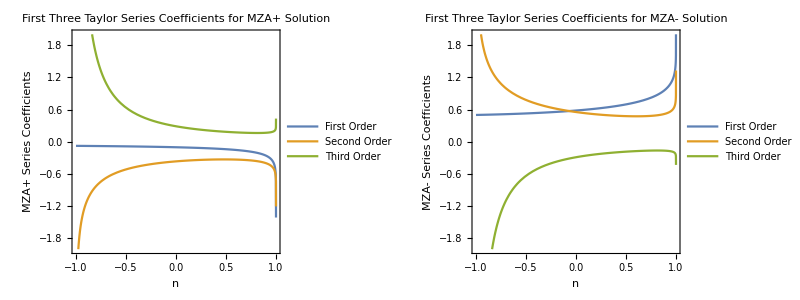

```mathematica
Grid@{{
Plot[
Evaluate@CoefficientList[
mzaSeries[n][[1]],
g1
],
{n,-1,1},Frame->True,ImageSize->Large,PlotLegends->Placed[{"First Order", "Second Order","Third Order"},{Right,Top}],PlotLabel->"First Three Taylor Series Coefficients for MZA+ Solution",PlotRange->{Automatic,{-2,2}},FrameLabel->{"n", "MZA+ Series Coefficients"}
],

Plot[
Evaluate@CoefficientList[
mzaSeries[n][[2]],
g1
],
{n,-1,1},Frame->True,ImageSize->Large,PlotLegends->Placed[{"First Order", "Second Order","Third Order"},{Right,Bottom}],PlotLabel->"First Three Taylor Series Coefficients for MZA- Solution",PlotRange->{Automatic,{-2,2}},FrameLabel->{"n", "MZA- Series Coefficients"}
]
}}
```

```mathematica
Limit[mzaSeries[n][[2]],n->0]
```

0.58121+0.552966 g1-0.288045 g1^2

Derivative of omega as a function of n

```mathematica
dOmegadN[n_,g1_]=D[
ConAxialSymOmegaNMZA[n,spectAbs2],
n
];
```

```mathematica
dOmegadNDataRaw=Table[
{n,g1,#}&/@dOmegadN[n,g1],
{n,-0.99,0.99,0.01},{g1,-10,10,1}
];//Quiet
```

```mathematica
dOmegadNDataRawShortRange=Table[
{n,g1,#}&/@dOmegadN[n,g1],
{n,-0.99,0.99,0.01},{g1,-1,1,0.1}
];//Quiet
```

```mathematica
dOmegadNData=Transpose[
Flatten[
dOmegadNDataRaw,
1
]
];//Quiet

dOmegadNDataShortRange=Transpose[
Flatten[
dOmegadNDataRawShortRange,
1
]
];//Quiet
```

```mathematica
ListPointPlot3D[
dOmegadNData,PlotRange->Full,ImageSize->Large,PlotLabel->"MZA Solutions",PlotLegends->{"MZA+","MZA-"},AxesLabel->{"n","g_1","dω/dn"}
]
```

-Graphics3D-

```mathematica
ListPointPlot3D[
dOmegadNDataShortRange,PlotRange->Full,ImageSize->Large,PlotLabel->"MZA Solutions",PlotLegends->{"MZA+","MZA-"},AxesLabel->{"n","g_1","dω/dn"},Filling->Axis
]
```

-Graphics3D-

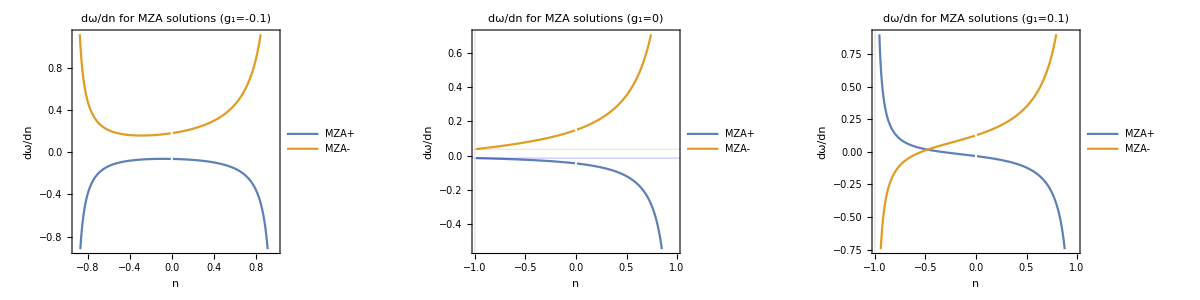

```mathematica
Grid@{{
ListPlot[
Transpose@Table[
{n,#}&/@dOmegadN[n,-0.1],
{n,-0.99,0.99,0.01}
],
Frame->True,ImageSize->Large,GridLines->{{-1},None},Joined->True,PlotLegends->Placed[{"MZA+","MZA-"},{Right,Top}],FrameLabel->{"n","dω/dn"},PlotLabel->"dω/dn for MZA solutions "<>"(g_1=-0.1)"
],
ListPlot[
Transpose@Table[
{n,#}&/@dOmegadN[n,0],
{n,-0.99,0.99,0.01}
],
Frame->True,ImageSize->Large,GridLines->{{-1},Transpose@{Limit[dOmegadN[n,0],n->-1],{Blue,Orange}}},Joined->True,PlotLegends->Placed[{"MZA+","MZA-"},{Right,Top}],FrameLabel->{"n","dω/dn"},PlotLabel->"dω/dn for MZA solutions "<>"(g_1=0)"
]
,
ListPlot[
Transpose@Table[
{n,#}&/@dOmegadN[n,0.1],
{n,-0.99,0.99,0.01}
],
Frame->True,ImageSize->Large,GridLines->{{-1},None},Joined->True,PlotLegends->Placed[{"MZA+","MZA-"},{Right,Top}],FrameLabel->{"n","dω/dn"},PlotLabel->"dω/dn for MZA solutions "<>"(g_1=0.1)"
]
}}//Quiet
```

```mathematica
Limit[dOmegadN[n,#],n->-1]&/@{-0.1,0,0.1}
```

{{ComplexInfinity,ComplexInfinity},{-0.0143723,0.0370502},{∞,-∞}}

```mathematica
Limit[dOmegadN[n,0.000001],n->-1]
```

{∞,-∞}